```mathematica
csv=Import["/home/faye/Documents/Homework/REU/SMALL/shared-code/Zeckendorf/Code/data/split-zero-one-two.csv"]
```

{1}
 |  |  |  |

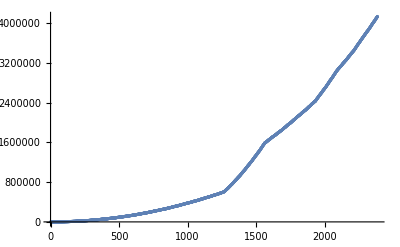

```mathematica
ListPlot[csv[[1]]]
```

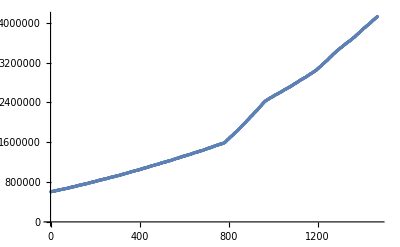

```mathematica
ListPlot[csv[[2]]]
```

```mathematica
ListPlot[csv[[3]]]
```

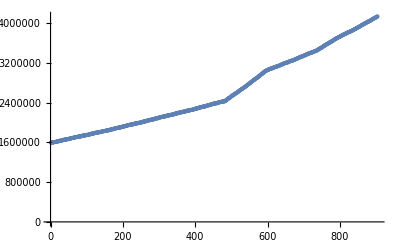

```mathematica
ListPlot[csv[[3]]]
```

-Graphics-

```mathematica
exhaustCsv=Import["/home/faye/Documents/Homework/REU/SMALL/shared-code/Zeckendorf/Code/data/split-exhaust.csv"];
```

```mathematica
quad=Fit[exhaustCsv[[1]],{1,x,x^2},x]
```

-188.795-0.657182 x+0.142942 x^2

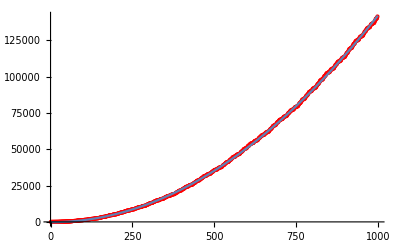

```mathematica
Show[ ListPlot[exhaustCsv[[1]], PlotStyle->Red], Plot[quad, {x, 0, 1000}]]
```

```mathematica
exhaustSmartCSV=Import["/home/faye/Documents/Homework/REU/SMALL/shared-code/Zeckendorf/Code/data/split-smart-exhaust-meow-8192.csv"];
```

```mathematica
quad=Fit[exhaustSmartCSV[[1]], {1, x, x^2}, x]
```

-809.381-1.2679 x+0.0952928 x^2

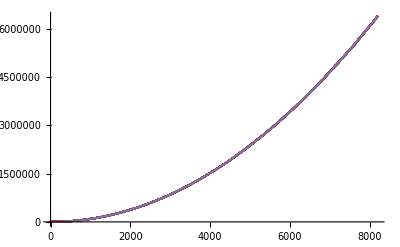
3 -Graphics-

```mathematica
Show[ListPlot[exhaustSmartCSV[[1]], PlotStyle->Red], Plot[quad, {x, 0, 8192}]]3
```

```mathematica
quad2=Fit[exhaustSmartCSV[[1]][[1;;1000]], {1, x, x^2}, x]
```

(-45.2973-1.1035 x+0.0945481 x^2)

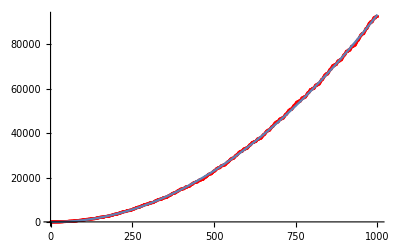

```mathematica
Show[ListPlot[exhaustSmartCSV[[1]][[1;;1000]], PlotStyle->Red], Plot[quad2, {x, 0, 1000}]]
```